```mathematica
$NumberMarks=False;
```

```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0,Reals];
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/.x->a;
weights[n_,x_]:=2/((1-x^2) legendreprime[n,x]^2);
```

```mathematica
SetDirectory["~/Dokumenty/FEM/hermes-dev/hermes2d/examples/neutronics/fixed-source/SN-first_attempt"];

(*how many terms should be generated*)
h=32;

(*what numerical precision is desired?*)
precision=16;

str=OpenWrite["lgvalues.txt"];
Write[str,"abcissae"];
Do[Write[str];Write[str,n];Write[str];
nlist=symboliclegendre[n,x];
xnlist=x/.nlist;
μ=Sort[xnlist,#1>#2&];
Do[Write[str,N[Part[μ,i],precision]],{i,Length[μ]}];,{n,2,h,2}];
Write[str,"weights"];
Do[Write[str];Write[str,n];Write[str];
slist:=symboliclegendre[n,x];
xslist=x/.slist;
μ=Sort[xslist,#1>#2&];
Do[Write[str,N[weights[n,Part[μ,i]],precision]],{i,Length[μ]}];,{n,2,h,2}];
Close[str];

ResetDirectory[];
```

```mathematica
xlist=x/.symboliclegendre[28,x];
```

```mathematica
μ=Sort[xlist,#1>#2&];
```

```mathematica
w=With[{n=Length[μ]},Table[weights[n,μ⟦i⟧],{i,1,n}]//N];
```

```mathematica
ω=Table[(2l-2i+1)/(2l)π/2,{l,1,Length[μ]/2},{i,1,l}];
```

```mathematica
pw=Table[w⟦l⟧/l,{l,1,Length[μ]/2}];
```

```mathematica
pw
```

{0.00912428,0.0105661,0.0109671,0.0110682,0.0110215,0.0108788,0.0106637,0.0103892,0.0100635,0.00969307,0.009283,0.00883798,0.0083624,0.0078605}

```mathematica
Total[Flatten@Table[pw⟦l⟧l,{l,1,Length[μ]/2}]]
```

1.

```mathematica
μ//N
```

{0.996442,0.981303,0.954259,0.915633,0.865893,0.805641,0.735611,0.656651,0.56972,0.475874,0.376252,0.272062,0.164569,0.0550793,-0.0550793,-0.164569,-0.272062,-0.376252,-0.475874,-0.56972,-0.656651,-0.735611,-0.805641,-0.865893,-0.915633,-0.954259,-0.981303,-0.996442}

```mathematica
Sum[pw⟦l⟧μ⟦l⟧^4,{l,1,Length[μ]/2},{i,1,4l}]
```

0.8

```mathematica
Sum[pw⟦Length[μ]-l+1⟧μ⟦l⟧^4,{l,Length[μ]/2+1,Length[μ]},{i,1,4(Length[μ]-l+1)}]
```

0.8

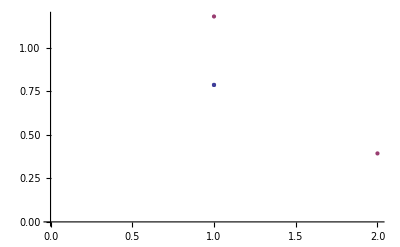

```mathematica
ListPlot[ω]
```

```mathematica
ξ=Map[Cos[#]&,ω,{2}];
η=Map[Sin[#]&,ω,{2}];
```

```mathematica
z={};
```

```mathematica
Do[z=Join[z,{{√(1-μ⟦l⟧^2)ξ⟦l,i⟧,√(1-μ⟦l⟧^2)η⟦l,i⟧,μ⟦l⟧}}],{l,1,Length[μ]/2},{i,1,l}]
```

```mathematica
ListPointPlot3D[z,PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
normals={{0,-1,0},{1,0,0},{-1,1,0}};
```

```mathematica
Reflected[Ω_,n_]:=Ω-2n(Ω.n);
```

```mathematica
zr1=Map[Reflected[#,normals⟦1⟧]&,N[z]];
zr2=Map[Reflected[#,normals⟦2⟧]&,N[z]];
zr3=Map[Reflected[#,normals⟦3⟧]&,N[z]];
```

```mathematica
ListPointPlot3D[{z⟦All,All⟧,zr2⟦All,All⟧},PlotRange->{{-1,1},{-1,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{z,zr1,zr2},PlotRange->{{-1,1},{-1,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
Q2[Ω_]:={-Ω⟦1⟧,Ω⟦2⟧,Ω⟦3⟧};
Q3[Ω_]:={-Ω⟦1⟧,-Ω⟦2⟧,Ω⟦3⟧};
Q4[Ω_]:={Ω⟦1⟧,-Ω⟦2⟧,Ω⟦3⟧};
```

```mathematica
zr2-Map[Q2[#]&,N[z]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
zr1-Map[Q4[#]&,N[z]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
Graphics3D[{
{Thickness[0.005],Line[z,VertexColors->ColorData["TemperatureMap"]/@Rescale@Range@Length@z]},
{Thickness[0.005],Line[zr2,VertexColors->ColorData["Rainbow"]/@Rescale@Range@Length@z]},
{Thickness[0.005],Line[Map[Q3[#]&,N[z]],VertexColors->ColorData["FruitPunchColors"]/@Rescale@Range@Length@z]},
{Thickness[0.005],Line[zr1,VertexColors->ColorData["GreenPinkTones"]/@Rescale@Range@Length@z]}},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Grid[{N@z,zr1,zr2},Frame->All]
```

{0.359475,0.359475,0.861136} | {0.359888,0.868846,0.339981} | {0.868846,0.359888,0.339981}
{0.359475,-0.359475,0.861136} | {0.359888,-0.868846,0.339981} | {0.868846,-0.359888,0.339981}
{-0.359475,0.359475,0.861136} | {-0.359888,0.868846,0.339981} | {-0.868846,0.359888,0.339981}